```mathematica
ClearAll["Global`*"]
```

# Preliminaries

Constants and parameters

```mathematica
logk0=1; "initial k to compute";
logkf=14; "final k to compute";
step=0.01; "step between each k";
bstep=1;
ms=1; "mass of ψ ODE";
H=1; "Hubble parameter";
γ=15; "amplitude of the feature of η";
δ=0.7; "feature width";
Nfeat=16; "e-fold of the feature center";
```

Lists of k’s

```mathematica
listk:=10^Range[logk0,logkf,step];
"listk:=Range[1, 10 ,1]";
listn0:=N@Subdivide[-4,27,Length[listk]-1];
"listn0:=N@Subdivide[-5,-5,Length[listk]-1]";
listnf :=N@Subdivide[34,34,Length[listk]-1];
"listnf :=N@Subdivide[15,15,Length[listk]-1]";
```

Lists to save the BC values

```mathematica
list=List[];"β_ζ1";
list2=List[]; "α_ζ1";
list3=List[]; "β_ζ2";
list4=List[]; "α_ζ2";
Plist=List[]; "Scalar power spectrum";
listpsi=List[]; "β_ψ1";
list2psi=List[]; "α_ψ1";
list3psi=List[]; "β_ψ2";
list4psi=List[]; "α_ψ2";
"Plistpsi=List[]";
```

Feature and modes (mass and massles, curvature and isocurvature) expressions

```mathematica
"η[t_]:=Exp[-(-Log[-t]-Nfeat)^2/(2*δ^2)]*γ";
η[t_]:=(HeavisideTheta[-Log[-t]+(-Nfeat+δ/2)]-HeavisideTheta[-Log[-t]+(-Nfeat-δ/2)])*γ; "turning rate/feature";
ζ[t_]=(1+ⅈ*k*t)*Exp[-ⅈ*k*t]; "curvature perturbation mode";
cζ[t_]:=(1-ⅈ*k*t)*Exp[ⅈ*k*t]; "conjugate of ζ mode";
"μ=Sqrt[ms^2+4*H*(η[t])^2]"; "entropic mass";
μ=1; "entropic mass";
ν=Sqrt[9/4-(μ/H)^2];
Hν[t_]:=N[HankelH1[ν,-k*t]]; "Hankel function for ψ expression";
cHν[t_]:=Conjugate[N[HankelH1[ν,-k*t]]]; "conjugate H_ν";
ψ[t_]:=ⅈ*Sqrt[π/2]*(-k*t)^(3/2)*Hν[t]; "isocurvature perturbation mode";
cψ[t_]:=-ⅈ*Sqrt[π/2]*(-k*t)^(3/2)*cHν[t];
```

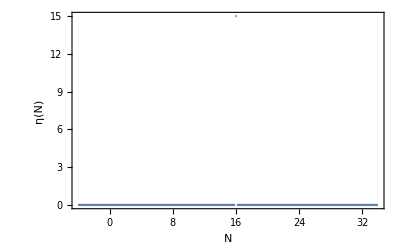

```mathematica
Plot[η[-Exp[-n]],{n,listn0[[1]], listnf[[-1]]},PlotRange->All,Frame ->True,FrameLabel->{Style["N", Black, FontSize->14],Style["η(N)", Black, FontSize->14]}]
```

We define the N_0 values when each mode oscillate rapidly and N_f is when all the modes freezed (this need to be a large value), hence we decide this values observing the ζ and ψ plots.

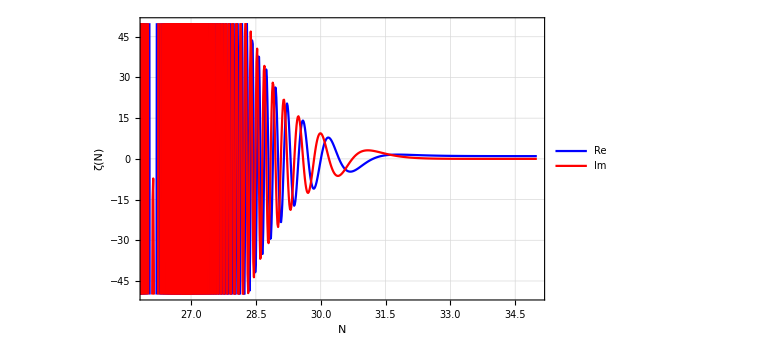

```mathematica
k=listk[[-1]];Plot[{Re[ζ[-Exp[-r]]],Im[ζ[-Exp[-r]]] },{r,-10,35},PlotRange->{{26,35},{-50,50}},PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["N", Black, FontSize->24],Style["ζ(N)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLegends->Placed[{"Re","Im"}, {0.9,0.8}]]
```

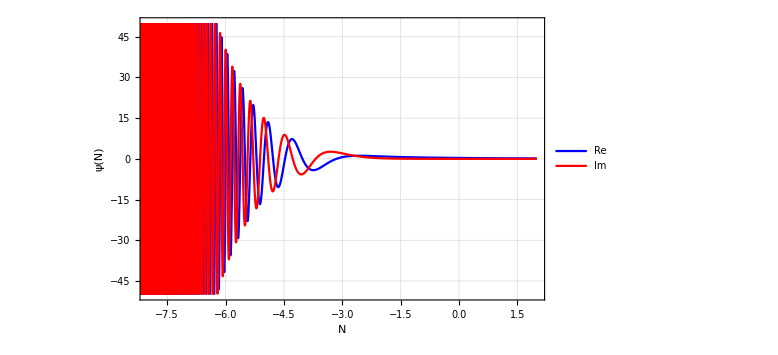

```mathematica
k=listk[[1]];Plot[{Re[ψ[-Exp[-r]]],Im[ψ[-Exp[-r]]] },{r,-10,2},PlotRange->{{-8,2},{-50,50}},PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["N", Black, FontSize->24],Style["ψ(N)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLegends->Placed[{"Re","Im"}, {0.9,0.8}]]
```

```mathematica
Clear[k]
```

Numerical ODEs solutions

We choose the values of the coefficients evaulated in the final e-fold (N_f), for each k.

In this block x1=α_ζ1, x2=β_ζ1      and      y1=α_ψ1, y2=β_ψ1

```mathematica
Do[k=listk[[i]];n0=listn0[[i]];nf=listnf[[i]];{s=NDSolve[{
x1'[t]==-ⅈ*η[t]/(k^3*t^3)*(D[cζ[t],t]*ψ[t]*y1[t]+D[cζ[t],t]*cψ[t]*y2[t]), 
x2'[t]==-ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*ψ[t]*y1[t]+-D[ζ[t],t]*cψ[t]*y2[t]),
y1'[t]==ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*cψ[t]*x1[t]+-D[cζ[t],t]*cψ[t]*x2[t]),
y2'[t]==ⅈ*η[t]/(k^3*t^3)*(D[ζ[t],t]*ψ[t]*x1[t]+D[cζ[t],t]*ψ[t]*x2[t]),
x1[-Exp[-n0]]==1, x2[-Exp[-n0]]==0, y1[-Exp[-n0]]==0, y2[-Exp[-n0]]==0},{x1,x2,y1,y2},{t,-Exp[-n0],-Exp[-nf]},MaxStepSize->10^(-3)],
 xx2[t_]:=x2[t]/.s, points1=Table[{k,n,xx2[-Exp[-n]]},{n,nf,nf,step}], nk=points1[[-1]],AppendTo[list,{nk[[1]],nk[[3]][[1]]}],
 xx1[t_]:=x1[t]/.s, points2=Table[{k,n,xx1[-Exp[-n]]},{n,nf,nf,step}], nk2=points2[[-1]],AppendTo[list2,{nk2[[1]],nk2[[3]][[1]]}],
 yy2[t_]:=y2[t]/.s, points1psi=Table[{k,n,yy2[-Exp[-n]]},{n,nf,nf,step}], nkpsi=points1psi[[-1]],AppendTo[listpsi,{nkpsi[[1]],nkpsi[[3]][[1]]}],
yy1[t_]:=y1[t]/.s, points2psi=Table[{k,n,yy1[-Exp[-n]]},{n,nf,nf,step}], nk2psi=points2psi[[-1]],AppendTo[list2psi,{nk2psi[[1]],nk2psi[[3]][[1]]}]},
{i, 1, Length[listk], 1}]
```

In this block x1=α_ζ2, x2=β_ζ2      and      y1=α_ψ2, y2=β_ψ2

```mathematica
Do[k=listk[[i]];n0=listn0[[i]];nf=listnf[[i]];{s2=NDSolve[{
x1'[t]==-ⅈ*η[t]/(k^3*t^3)*(D[cζ[t],t]*ψ[t]*y1[t]+D[cζ[t],t]*cψ[t]*y2[t]),
x2'[t]==-ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*ψ[t]*y1[t]+-D[ζ[t],t]*cψ[t]*y2[t]),y1'[t]==ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*cψ[t]*x1[t]+-D[cζ[t],t]*cψ[t]*x2[t]),
y2'[t]==ⅈ*η[t]/(k^3*t^3)*(D[ζ[t],t]*ψ[t]*x1[t]+D[cζ[t],t]*ψ[t]*x2[t]), 
x1[-Exp[-n0]]==0, x2[-Exp[-n0]]==0, y1[-Exp[-n0]]==1, y2[-Exp[-n0]]==0},{x1,x2,y1,y2},{t,-Exp[-n0],-Exp[-nf]},MaxStepSize->10^(-3)], 
xx22[t_]:=x2[t]/.s2, points3=Table[{k,n,xx22[-Exp[-n]]},{n,nf,nf,step}], nk3=points3[[-1]],AppendTo[list3,{nk3[[1]],nk3[[3]][[1]]}],
xx11[t_]:=x1[t]/.s2, points4=Table[{k,n,xx11[-Exp[-n]]},{n,nf,nf,step}], nk4=points4[[-1]],AppendTo[list4,{nk4[[1]],nk4[[3]][[1]]}],
yy22[t_]:=y2[t]/.s2, points3psi=Table[{k,n,yy22[-Exp[-n]]},{n,nf,nf,step}], nk3psi=points3psi[[-1]],AppendTo[list3psi,{nk3psi[[1]],nk3psi[[3]][[1]]}],
yy11[t_]:=y1[t]/.s2, points4psi=Table[{k,n,yy11[-Exp[-n]]},{n,nf,nf,step}], nk4psi=points4psi[[-1]],AppendTo[list4psi,{nk4psi[[1]],nk4psi[[3]][[1]]}] },
{i, 1, Length[listk], 1}]
```

Plots

Power spectrum

To each k we compute the power spectrum

```mathematica
Do[AppendTo[Plist,List[list[[i]][[1]],(Abs[list[[i]][[2]]+list2[[i]][[2]]])^2+(Abs[list3[[i]][[2]]+ list4[[i]][[2]]])^2]],{i,1,Length[listk],1}]
Plist;
```

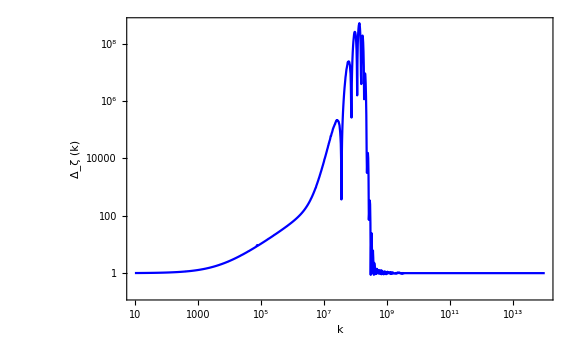

```mathematica
ListLogLogPlot[{Plist}, PlotStyle->Blue, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, Italic,FontSize->24,FontFamily->"Cambria"],Text@Style["Δ_ζ \!\(\*StyleBox[\"(k)\",\nFontSlant->\"Italic\"]\)",Black, FontSize->24,FontFamily->"Cambria"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotRange->{{10^logk0,10^logkf},Automatic}, Joined->True]
```

```mathematica
Export["/Users/javier/Documents/research/CosmoSur/codes/Pzeta3.fits",Plist]
```

/Users/javier/Documents/research/CosmoSur/codes/Pzeta3.fits

Bogoliubov coefficientes

```mathematica
listalpha1R := List[];
listalpha1I := List[];
listbeta1R := List[];
listbeta1I := List[];
listalpha2R := List[];
listalpha2I := List[];
listbeta2R := List[];
listbeta2I := List[];
Do[AppendTo[listalpha1R,List[list2[[i]][[1]],Re[list2[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listalpha1I,List[list2[[i]][[1]],Im[list2[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listbeta1R,List[list[[i]][[1]],Re[list[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listbeta1I,List[list[[i]][[1]],Im[list[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listalpha2R,List[list4[[i]][[1]],Re[list4[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listalpha2I,List[list4[[i]][[1]],Im[list4[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listbeta2R,List[list3[[i]][[1]],Re[list3[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listbeta2I,List[list3[[i]][[1]],Im[list3[[i]][[2]]]]],{i,1,Length[listk],1}];
```

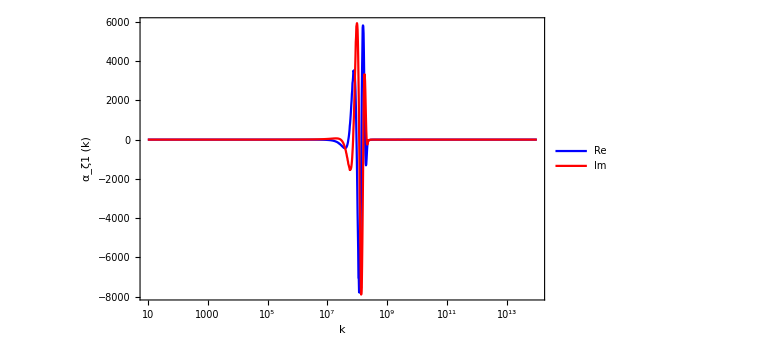

```mathematica
ListLogLinearPlot[{listalpha1R,listalpha1I}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, Italic,FontSize->24,FontFamily->"Cambria"],Text@Style["α_ζ1 \!\(\*StyleBox[\"(k)\",\nFontSlant->\"Italic\"]\)",Black, FontSize->24,FontFamily->"Cambria"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotRange->{{10^logk0,10^logkf},All}, Joined->True,PlotLegends->Placed[{"Re","Im"}, {0.9,0.67}]]
```

```mathematica
Export["/Users/javier/Documents/research/CosmoSur/codes/alphazeta1R3.fits",listalpha1R];
Export["/Users/javier/Documents/research/CosmoSur/codes/alphazeta1I3.fits",listalpha1I];
```

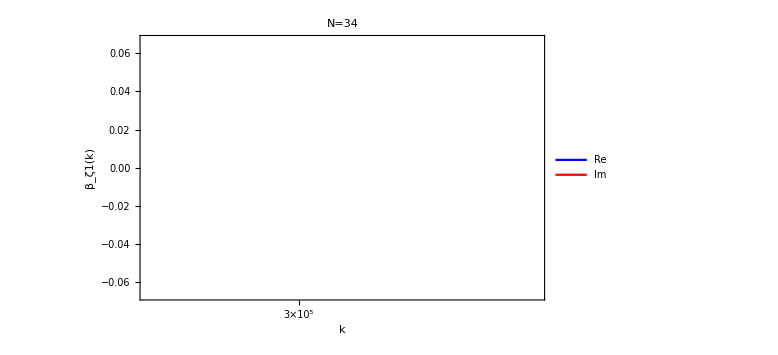

```mathematica
p2=ListLogLinearPlot[{listbeta1R,listbeta1I}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["β_ζ1(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{2.5*10^5,4*10^5},{-1/15, 1/15}}, Joined->True,PlotLegends->Placed[{"Re","Im"}, {0.9,0.8}]]
```

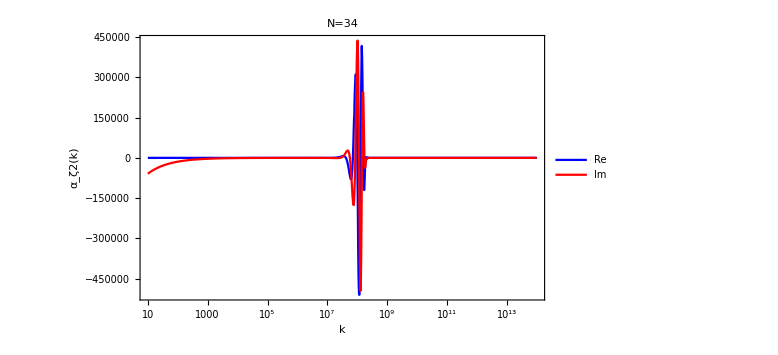

```mathematica
p3=ListLogLinearPlot[{listalpha2R,listalpha2I}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["α_ζ2(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{10^logk0,10^logkf},All}, Joined->True,PlotLegends->Placed[{"Re","Im"}, {0.9,0.67}]]
```

```mathematica
ListLogLinearPlot[{listbeta2R,listbeta2I}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["β_ζ2(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{10^logk0,10^logkf},All}, Joined->True,PlotLegends->Placed[{"Re","Im"}, {0.9,0.8}]]
```

-Graphics-

```mathematica
listalpha1Rpsi := List[];
listalpha1Ipsi := List[];
listbeta1Rpsi := List[];
listbeta1Ipsi := List[];
listalpha2Rpsi := List[];
listalpha2Ipsi := List[];
listbeta2Rpsi := List[];
listbeta2Ipsi := List[];
Do[AppendTo[listalpha1Rpsi,List[list2psi[[i]][[1]],Re[list2psi[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listalpha1Ipsi,List[list2psi[[i]][[1]],Im[list2psi[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listbeta1Rpsi,List[listpsi[[i]][[1]],Re[listpsi[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listbeta1Ipsi,List[listpsi[[i]][[1]],Im[listpsi[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listalpha2Rpsi,List[list4psi[[i]][[1]],Re[list4psi[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listalpha2Ipsi,List[list4psi[[i]][[1]],Im[list4psi[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listbeta2Rpsi,List[list3psi[[i]][[1]],Re[list3psi[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listbeta2Ipsi,List[list3psi[[i]][[1]],Im[list3psi[[i]][[2]]]]],{i,1,Length[listk],1}];
```

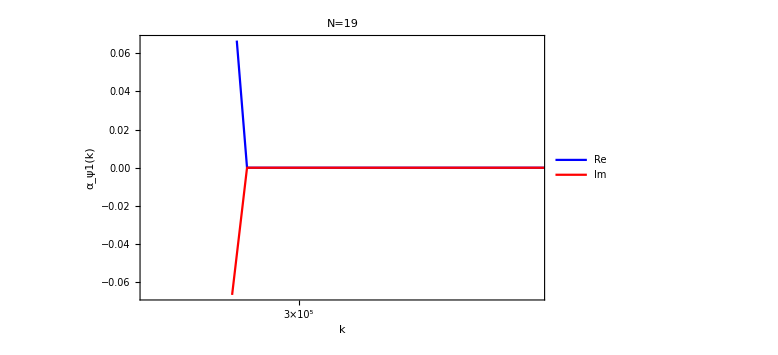

```mathematica
ListLogLinearPlot[{listalpha1Rpsi,listalpha1Ipsi}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["α_ψ1(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{2.5*10^5,4*10^5},{-1/15, 1/15}}, Joined->True,PlotLegends->Placed[{"Re","Im"}, {0.9,0.67}]]
```

```mathematica
p2psi=ListLogLinearPlot[{listbeta1Rpsi,listbeta1Ipsi}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["β_ψ1(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{10^logk0,10^logkf},Full}, Joined->True,PlotLegends->Placed[{"Re","Im"}, {0.9,0.8}]]
```

-Graphics-

```mathematica
p3psi=ListLogLinearPlot[{listalpha2Rpsi,listalpha2Ipsi}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["α_ψ2(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{10^logk0,10^logkf},All}, Joined->True,PlotLegends->Placed[{"Re","Im"}, {0.9,0.67}]]
```

-Graphics-

```mathematica
p4psi=ListLogLinearPlot[{listbeta2Rpsi,listbeta2Ipsi}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["β_ψ2(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{10^logk0,10^logkf},All}, Joined->True,PlotLegends->Placed[{"Re","Im"}, {0.9,0.8}]]
```

-Graphics-

```mathematica
Plist1:=List[]
Plist2:=List[]
```

```mathematica
Do[AppendTo[Plist1,List[list[[i]][[1]],(Abs[list[[i]][[2]]+list2[[i]][[2]]])^2]],{i,1,Length[listk],1}]
Do[AppendTo[Plist2,List[list[[i]][[1]],(Abs[list3[[i]][[2]]+ list4[[i]][[2]]])^2]],{i,1,Length[listk],1}]
```

```mathematica
ListLogLinearPlot[{Plist1,Plist2}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["\!\(\*SuperscriptBox[\(|α_ζi+β_ζi|\), \(2\)]\)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{10^logk0,10^logkf},Full}, Joined->True,PlotLegends->Placed[{"Mode 1","Mode 2"}, {0.9,0.8}]]
```

-Graphics-

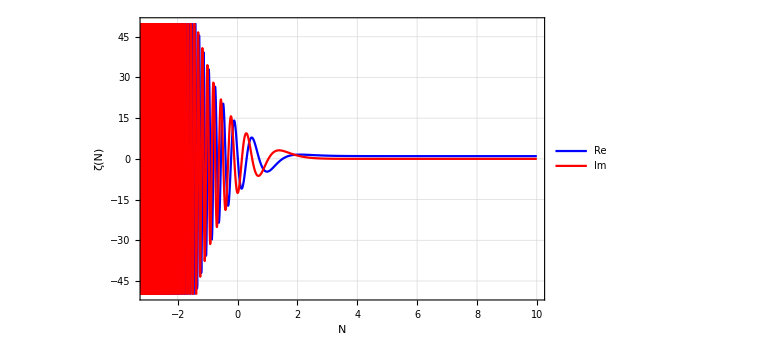

```mathematica
k=listk[[-1]];Plot[{Re[ζ[-Exp[-r]]],Im[ζ[-Exp[-r]]] },{r,-20,10},PlotRange->{{-3,10},{-50,50}},PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["N", Black, FontSize->24],Style["ζ(N)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLegends->Placed[{"Re","Im"}, {0.9,0.8}]]
```

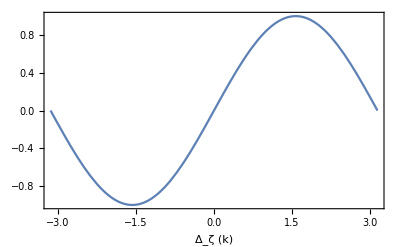

```mathematica
Plot[Sin[x], {x,-Pi,Pi}, Frame->True, FrameStyle->Gray, BaseStyle->{FontFamily->"Latin Modern Roman"},FrameLabel->{Text@Style["Δ_ζ \!\(\*StyleBox[\"(k)\",\nFontSlant->\"Italic\"]\)"]}]
```